# Lab 02 : Electric Fields of Various Electrode Geometries

Charlie Bushman
Phys 235 Lab 02
04-09-19

## Section A : Parallel Plate Capacitor

Using two flat parallel electrodes, we will find the charge on them for given input voltages. The voltages will be supplied by a function generator set to 16 kHz and the output voltages from the parallel plate capacitor is amplified then measured by an oscilloscope.

### Section A .1 : Amplifier Proportionality Constant

The amplifier we are using has a unique proportionality constant (in the realm of 0.08 V output for 1pC input charge) which we must determine before using the amplifier. To do this, we use a series of test capacitors of known capacitances (1 pF to 22 pF) and measure output voltages for a constant input voltage. This gives us the data in capFxnVoltAmpVolt below and allows us to find the proportionality constant of the amplifier.

```mathematica
(*Table 1*)
(*Note the reordering: Capacitance, Subscript[V, fg], Subscript[V, a]*)
capFxnVoltAmpfVolt={{22*10^-12,3.68,7.36},{15*10^-12,3.68,5.04},{10*10^-12,3.68,3.36},{5*10^-12,3.68,1.88},{2*10^-12,3.68,0.728},{1*10^-12,3.68,0.396}};
capFxnVoltAmpfVolt//N//TableForm
(*Table 3*)
chrgAmpfVolt=Table[{capFxnVoltAmpfVolt[[i,1]]*capFxnVoltAmpfVolt[[i,2]],capFxnVoltAmpfVolt[[i,3]]},{i,1,Length[capFxnVoltAmpfVolt]}];
chrgAmpfVolt//N//TableForm
```

2.2×10^-11 | 3.68 | 7.36
1.5×10^-11 | 3.68 | 5.04
1.×10^-11 | 3.68 | 3.36
5.×10^-12 | 3.68 | 1.88
2.×10^-12 | 3.68 | 0.728
1.×10^-12 | 3.68 | 0.396

8.096×10^-11 | 7.36
5.52×10^-11 | 5.04
3.68×10^-11 | 3.36
1.84×10^-11 | 1.88
7.36×10^-12 | 0.728
3.68×10^-12 | 0.396

```mathematica
(*Associated uncertainties with capacitance, output voltage, and charge*)
δC={1.1*10^-12,0.75*10^-12,0.5*10^-12,0.25*10^-12,0.25*10^-12,0.25*10^-12};
δVfg=Table[0.04,{i,1,Length[δC]}];
δQ=Table[Sqrt[capFxnVoltAmpfVolt[[i,2]]^2*δC[[i]]^2+capFxnVoltAmpfVolt[[i,1]]^2*δVfg[[i]]^2],{i,1,Length[δC]}];
δQ//N//TableForm
```

4.14255×10^-12
2.82446×10^-12
1.88298×10^-12
9.41488×10^-13
9.23472×10^-13
9.20869×10^-13

0.0914559

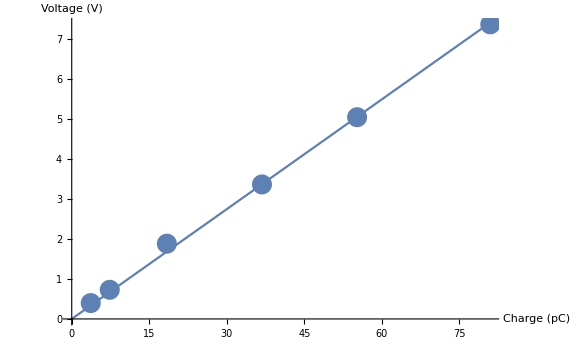

```mathematica
chrgAmpfVoltAdjusted=Table[{chrgAmpfVolt[[i,1]]*10^12,chrgAmpfVolt[[i,2]]},{i,1,Length[chrgAmpfVolt]}];
chrgAmpfVoltFit=Fit[chrgAmpfVoltAdjusted,{x},x];
propConst=chrgAmpfVoltFit[[1]]
Show[ListPlot[chrgAmpfVoltAdjusted,Axes->True,AxesLabel->{"Charge (pC)","Voltage (V)"},PlotStyle->PointSize[0.025],ImageSize->Large],Plot[chrgAmpfVoltFit,{x,0,83}]]
```

### Section A .2 : Capacitance of Parallel Plates

With our proportionality constant now stored in propConst, we can move on to the task at hand which is determining the capacitance of our parallel plates. To do this, we setup the plates at a distance d from each other and apply a constant voltage through the function generator and then measure the output voltage through the amplifier. This output voltage corresponds to a charge on the plates via our proportionality constant. We can then use the equation C = Q/V where C is the capacitance, Q is the charge on the plates, and V is the voltage applied to the plates to determine the capacitance.

```mathematica
(*Table 2*)
distVolt={{0.014,1.42},{0.033,0.564},{0.050,0.384},{0.069,0.274},{0.089,0.212},{0.109,0.172}};
invDistVolt=Table[{1/distVolt[[i,1]],distVolt[[i,2]]},{i,1,Length[distVolt]}];
invDistVolt//TableForm
```

71.4286 | 1.42
30.303 | 0.564
20. | 0.384
14.4928 | 0.274
11.236 | 0.212
9.17431 | 0.172

```mathematica
δd=0.001;
δV={0.02,0.004,0.004,0.004,0.002,0.002};
uncInvDistVolt=Table[{δd/distVolt[[i,1]]^2,δV[[i]]},{i,1,Length[distVolt]}];
uncInvDistVolt//TableForm
```

5.10204 | 0.02
0.918274 | 0.004
0.4 | 0.004
0.21004 | 0.004
0.126247 | 0.002
0.084168 | 0.002

-0.0187346+0.0200365 x

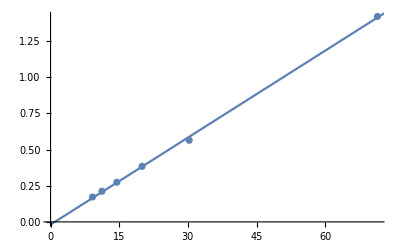

```mathematica
distVoltFit=Fit[invDistVolt,{1,x},x]
Show[ListPlot[invDistVolt],Plot[distVoltFit,{x,0,75}]]
```